# Trap Calculations

New Notebook for CAL to calculate mangetic fields, magnetic field minima, and trap frequencies for initial and relaxed fields. All functions have been defined in the CAL_functions package.   

Contents: 
Constants & Functions
	Coil/Chip Info
	Functions
SM3 AI capable chip calculations
	Chip/System notes
	Magnetic Field Calc and Traps

Written by : Maren Mossman (MM) and Peter Engels (PE).  
Last Edited : 01.22.2021 (MM)

## Upload Constants & Functions

```mathematica
SetDirectory[NotebookDirectory[]] ;
Get["CAL_functions_murphree.m"]
(* Get Bates functions: *)
Get["BatesToMEConverter.m"]
Get["SMThreeChipModel.m"]
Get["SMThreeTraps.m"]

(* For a list of functions/constants call *)
(*?"CALfunctions`*"*)
(* Make sure that you update the path to the CAL functions mathematica package! *)

FileNames["*","/Users/marenmossman/Desktop/NASA Project/mathematica/SM3"];
?"CALfunctions`*"
```

```mathematica
?"BatesToMEConverter`*"
```

## Coil/Chip Info

#### Bias cage parameters

Changed the separation of the 
X-bias coils from 1.181 to 1.19105 (255 microns) 
Y-bias coils from 2.362 to 2.3572 (123 microns)
Z-bias coils from 3.228 to 3.10325 (3.169 mm) <-- Less believable
to match the measurements/calibrations from CQ.

```mathematica
(* 
In these lists, we have: 
 wiredia = coils[[1]];
	current = coils[[2]];
	width = coils[[3]];
	height = coils[[4]];
	coilspacing = coils[[5]];
	hmax = coils[[6]];
	rmax = coils[[7]]; 
	offset = coils[[8]];
*)

(*?"CALfunctions`YbiasCoils"
?"CALfunctions`ZbiasCoils"
?"CALfunctions`TransferCoils"
?"CALfunctions`MOTCoils"
?"CALfunctions`FFCoils"*)
```

#### SM3 Chip

```mathematica
(* 
When recording the chip design, you want to state the parameters for the entire coil. For the wires with 3 parts, you typically have a wire in the y-direction, the x-direction, and another y-direction. The order of these wires appear should be in the direction of source to sink, labeled in page 7 of CAL3A_chip&drivers_200128.pdf from JPL. The way in which the numbers are recorded is, e.g. a coil in the Y-direction: 
{x-fixed coordinate, y-start coordinate, y-end coordinate}
*)

(* 
Can only use 1 set of wires/coils per driver;
Driver 1: Z1, L2, T2;
Driver 2: Z2, L1, FF;
Driver 3: H-wires;
*)

(*?"CALfunctions`Za"
?"CALfunctions`Zb"
?"CALfunctions`La"
?"CALfunctions`Lb"
?"CALfunctions`Tb"
?"CALfunctions`Ha"
?"CALfunctions`Hb"*)
```

## Functions

### Magnetic Field Functions

General Notes

All B-field functions for square bias coils, chip, and breit-rabi corrections.

External Bias Fields

IMPORTANT: These parameters were found with the CAL schematics and spec sheets and should be fixed for each copy of the CAL apparatus with exception to the ϵ variable parameter.  Do Not Change the "*Coils[I_]" list functions in the CAL_functions package!

Below, find the coordinate transformation needed to accurately model the coils. Parameter ϵ, defined by default as 0, is used to take into consideration any offset of the atom chip (since it can vary for each different copy of the CAL system) - plan to use this parameter in real time to adjust system parameters.

Frequencies found for the external bias fields are harmonic enough that during calculations and the trajectory simulations, the acceleration is calculated using the frequencies because it is faster than using the real field.

External bias field coils can be run up to 8.0A, though for heating purposes, it may be best to not run them too high for too long.

The Transfer Coils and FF coils are the only ones that are centered at the atom chip.  The y-bias coils are centered 0.4525 in (11.5 mm) below the chip and the MOT coils are centered 0.591 in (15 mm) below the chip.  Therefore, if your y-bias field current is higher than your transfer current, you will start to pull the minimum away from the zero gradient of the field. Recommended to make use of the z-bias coils to recenter things to move the magnetic zero.

Each set of coils has a list consisting of: {wire diameter, current (variable), inner width, inner height, inner coil spacing, number of windings out, number of windings up, z-offset from the atom chip}. These lists can be found in the CAL_functions package.

Set up where coordinates are defined wrt atom chip coordinates (x, y, z):
- Transfer, MOT, and FF coils are oriented in the same direction (z’ = x, y’ = z, x’ = y). 
- The transfer coils and the FF coils are centered on the atom chip +/- ϵ.   
- The Y-bias coils are offset and rotated such that (z’’ = x’, y’’ = y’, x’’ = -z’). 
- The Z-bias coils are offset and rotated such that (z’’’ = y’, x’’’ = x’, y’’’ = -z’).

Magnetic field of a square wire loop

NOTES:
- All coils point with their axis into the z direction. 
- Each coil is a list consisting of the following elements found in "Coil Information": {width,height,x,y,z,current}. 
- Lengths are in meters,currents in Amps. 
- Width is in x direction, Height in y direction.

Note that this calculates the magnetic field of rectangular solenoids in Tesla.

z’ = x-direction on chip
x’ = y-direction on chip
y’ = z-direction from chip

Field Functions
Bz[], By[], Bx[], BxField[], ByField[], BzField[], BxSum[], BySum[], BzSum[], FieldMag[], BiasCoils[]

Coil Lists
YbiasCoils, ZbiasCoils, TransferCoils, MOTCoils, FFCoils

Atom Chip Fields

The field functions for the chip traces take Biot-Savart of a finite length of wire, either in the x-direction (Xwire) or the y-direction (Ywire).  The input for these two functions are the height away from the inner surface of the chip that is 100 microns thick and the coordinates of the wire (position and length). This code was developed by the team at JPL and sent to users for the CAL project.  It has since been modified by MM for changes to the flight system.

These functions have been updated to calculate the field in Tesla.

Field Functions
Xwire[], Ywire[], ChipTrapField[], ChipTrapFieldFAST[] (Use the FAST functions to use the constant magnetic fields)

### Magnetic Field Tests

Note : When running these tests, be sure to use "None" for the Trap Parameters. Otherwise, if you try to calculate the B - field at {0, 0, 0} (the chip center), you will return a slew of 1/0 errors.

```mathematica
{EnergyBR[2,2,31.05Gauss,"Rb87"]-EnergyBR[2,1,31.05Gauss,"Rb87"]}/hPlanck/MHz
{EnergyBR[2,1,31.05Gauss,"Rb87"]-EnergyBR[2,0,31.05Gauss,"Rb87"]}/hPlanck/MHz
{(EnergyBR[2,2,31.05Gauss,"Rb87"]-EnergyBR[2,1,31.05Gauss,"Rb87"])-(EnergyBR[2,1,31.05Gauss,"Rb87"]-EnergyBR[2,0,31.05Gauss,"Rb87"])}/hPlanck/MHz
```

{21.5153}

{21.6513}

{-0.13599}

Currents list={iD1, iD2, iD3, iT, iM, iY, iZ, iFF}; magnetic field calibrations: Xbias=40.625G, Ybias=14.286G, Zbias=10.3675G

```mathematica
Reference={0,0,0,0.22,0,-2.567,0.150,0};
TrapParams={"Rb87",2,2,"None","None","None"};
(*(ChipTrapField[0,0,0,Reference,TrapParams]/Gauss);*)
XbiasGperA=(ChipTrapField[0,0,0,{0,0,0,1,0,0,0,0},TrapParams]/Gauss)
MOTGperA=(ChipTrapField[0,0,0,{0,0,0,0,1,0,0,0},TrapParams]/Gauss)
YbiasGperA=(ChipTrapField[0,0,0,{0,0,0,0,0,1,0,0},TrapParams]/Gauss)
ZbiasGperA= (ChipTrapField[0,0,0,{0,0,0,0,0,0,1,0},TrapParams]/Gauss)
FFGperA =(ChipTrapField[0,0,0,{0,0,0,0,0,0,0,1},TrapParams]/Gauss)
(*((MagTrapField[0,0,0.101mm,{0,0,0,1,0,0,0,0},TrapParams]-MagTrapField[0,0,0.001mm,{0,0,0,1,0,0,0,0},TrapParams])/(0.1mm))*100*)
```

10000 ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None.

10000 ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None.

10000 ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None.

«2 more identical outputs»

Part::partw: Part 8 of {0,0,0,0.,0,0,0} does not exist.

Part::partw: Part 8 of {0,0,0,0.25,0,0,0} does not exist.

Part::partw: Part 8 of {0,0,0,0.5,0,0,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

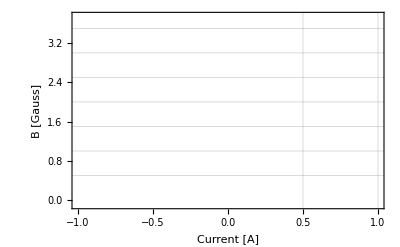

```mathematica
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,x,0,0,0},TrapParams]/Gauss},{x,0,3,0.25}],PlotRange->{-0.1,3.75},Frame-> True,GridLines-> {{0.5,1,1.5,2,2.5,3}, {0.5,1,1.5,2,2.5,3,3.5}},FrameLabel-> {"Current [A]","B [Gauss]"},PlotStyle->Yellow,PlotMarkers->{Automatic,12},Joined->True]
```

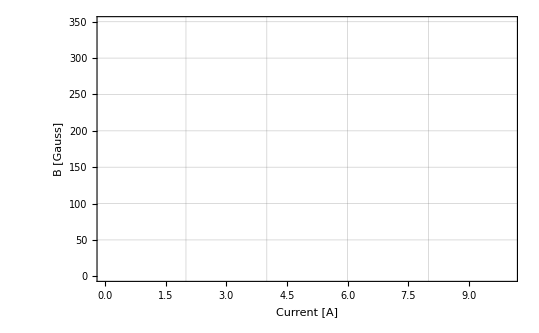

```mathematica
Show[
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,x,0,0,0,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotRange->{{0,10},{0,350}},Frame-> True,GridLines-> {{2,4,6,8}, {50,100,150,200,250,300,350}},FrameLabel-> {"Current [A]","B [Gauss]"},PlotStyle->Red,PlotMarkers->{Automatic,12},Joined->True],
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,0,x,0,0,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotStyle->Blue,PlotMarkers->{Automatic,12},Joined->True],
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,0,0,x,0,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotStyle->Green,PlotMarkers->{Automatic,12},Joined->True],
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,0,0,0,x,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotStyle->Orange,PlotMarkers->{Automatic,12},Joined->True]
]
```

## SM3 AI capable chip calculations

## Chip/System Notes (SM3 AI capable chip)

Note: 
- Chosen coordinate system: "x" is the direction of the main chip wire, and "y" is the direction current flows along the cross wire. Coordinates of the wire are defined from left to right on the image Dave sent (ambient side) (i.e. Example = {{left y wire coord}, {main x wire coord}, {right y wire coord}}). 
- Z wires are current limited to 3.5 A (Z1 - 1.0 A flight, Z2 - 2.75 A flight)
- H wires are current limited to 5.0 A (H wires - 2.75 A flight)

MOT and Transfer coils can handle up to 8.0 A, while the Y and Z wires can run up to 3.0 A.

Fast Feshbach (FF) coils are now run by current driver 2, which means that they cannot be running at the same time as Z2 and L1.

Note: For the relationship between the CAL table system and the current that goes into the wires:

X-bias coils: 0.081 A == 10 mV

Y-bias coils: 0.029 A == 10 mV

Z-bias coils: 0.030 A == 10 mV

Z1 (L) chip: 0.85 A == 0.243 V

Z2 (Z) chip: 2.4 A == -0.686 V

H wires chip: 2.3 A == 0.46 V

-Graphics-

## Magnetic Field Calculations and Traps

### Notes

In this section, we define functions to calculate features of the magnetic traps with the atom chip and the megnetic fields for the Feshbach resonances. All but the ChipTrapField functions can be found in the CALfunctions` package, due to changes in which traces you want to use.

Note: Members of the team at JPL have said they use L2, Z2, and the H-wires to generate a BEC, so we use these as a test set.

Field Functions
ChipTrapField[] - Use for precise calculations SM3 AI chip (uses real fields)
ChipTrapFieldFAST[] - Use for fast calculations SM3 AI chip (uses approximate fields)

### Trap Parameters

#### Set your currents here

Make a list of 8 currents in the following order: 

{I_driver1, I_driver2, I_driver3, I_transfercoils, I_MOTcoils, I_ybiascoils, I_zbiascoils, I_FFcoils} ***

*** For reference: Dave Aveline (JPL) says that with SM3 AI chip, {0.85,2.40,2.30,-0.222,0,2.545,-0.160,0}*A, they get a BEC with Rb-87 in gravity at the GTB.

```mathematica
(* Confirmed traps with the flight apparatus, current provided by Dave Aveline on April 24, 2019. *)
iLb=0.851;
iZb =2.401;
iH = 2.300;
iTx = -0.220;
iYy = 2.567;
iZz =-0.150;
(*currents = {iLb,iZb,iH,iTx,0,iYy,iZz,0}*A; *)
```

```mathematica
currents = convertCurrentsBToME@convertCALTableToCurrents@tableZHbB3
currentsTemp=currents;
```

{0.,2.425,2.6,0.048,0.,0.2488,0.300285,0.}

```mathematica
currents=({#1,#2,#3,-#4,#5,#6,-#7,#8}&@@currentsTemp)
```

{0.,2.425,2.6,-0.048,0.,0.2488,-0.300285,0.}

#### State how you are preparing your atoms in (initial trap)

Note : All atoms are prepared in the | 2, 2 > state on CAL for both Rb and K. All minimizing functions and trap frequencies are found using the Breit - Rabi energy calculation, so specifying the F and mF states in your trap parameters is very important for calculating the trap frequencies. For microgravity, set g = 0. D1, D2, D3 are the drivers 1, 2, and 3, respectively.

```mathematica
grav=0;
yguess = -0.5mm;
F=2;
mF=2;
isotope="Rb87";
D1="L2";
D2="Z2";
D3 = "H";
TrapParams = {isotope,F,mF,D1,D2,D3}
```

{Rb87,2,2,L2,Z2,H}

#### Test whether or not the trap parameters you entered above are valid!

If your trap parameters are invalid, the test function will return with an error function.

```mathematica
Btest = ChipTrapFieldFAST[0,yguess,0.2mm,currents,TrapParams]
Btest2 = ChipTrapField[0,yguess,0.2mm,currents,TrapParams]
```

0.00204374

0.00204933

#### Calculate minima, magnetic fields and frequencies using FAST functions

```mathematica
{xi,yi,zi}=zminFAST[currents,TrapParams,grav,yguess]
Bmin = ChipTrapFieldFAST[xi,yi,zi,currents,TrapParams]/Gauss
Trapbottom ={EnergyBR[2,2,Bmin*Gauss,"Rb87"]-EnergyBR[2,1,Bmin*Gauss,"Rb87"]}/hPlanck/MHz
Freq =  ChipTrapFreqFAST[xi,yi,zi,currents,TrapParams,0]
```

{0.00004132310487,-0.0003245438479,0.0006441305087}

5.0184

{3.50534}

{18.4923,26.1853,31.2974}

```mathematica
Chop@convertCoorMEToB[{xi,yi,zi}]*10^6
```

{61.8146,-500.,792.893}

#### Calculate minima, magnetic fields and frequencies using full fields (WARNING: VERY SLOW - takes about a minute to run)

```mathematica
zminRestricted[currents_,trapparams_,gravity_,ylim_] := Module[{xi,yi,zi,x,y,z,zlim},
Which[gravity==0,zlim=0.8mm,
gravity==1,zlim=0.5mm];
{xi,yi,zi} = NMinimize[{1000*PE[x,y,z,currents,trapparams,gravity]/kB,-0.2mm<x<0.2mm && ylim-0.2mm<y<ylim+0.2mm &&0.003mm<z<zlim},{x,y,z},WorkingPrecision->10][[2]];
xi = xi[[2]];
yi = yi[[2]];
zi = zi[[2]];
Return[{xi,yi,zi}]
];
{xi,yi,zi}=zminRestricted[currents,TrapParams,grav,yguess]
```

{0.00002654572144,-0.0003273715569,0.0007047339363}

{0.00002654572144,0.000672628,0.0007047339363}

```mathematica
Chop@convertCoorMEToB@{xi,yi,zi}*10^6
```

{26.54572144,672.628,704.7339363}

{0.0005,0.001,0.003}

```mathematica
(*{xi,yi,zi}=testPt*)(*zmin[currents,TrapParams,grav,yguess]*)
Bmin = ChipTrapField[xi,yi,zi,currents,TrapParams]/Gauss
Trapbottom ={EnergyBR[2,2,Bmin*Gauss,"Rb87"]-EnergyBR[2,1,Bmin*Gauss,"Rb87"]}/hPlanck/MHz
(* LACKS GRAVITY VARIABLE INCLUDED IN ChipTrapFreqFAST *)
Freq =  ChipTrapFreq[xi,yi,zi,currents,TrapParams]
```

5.08891

{3.55452}

{17.4572,24.4154,27.9591}

```mathematica
Chop@convertCoorMEToB[{xi,yi,zi}]*10^6
```

{500.,500.,3000.}

```mathematica
Bmin=5.02;
{EnergyBR[2,2,Bmin*Gauss,"Rb87"]-EnergyBR[2,1,Bmin*Gauss,"Rb87"]}/hPlanck/MHz
```

{3.50646}

#### Check Mag Fields

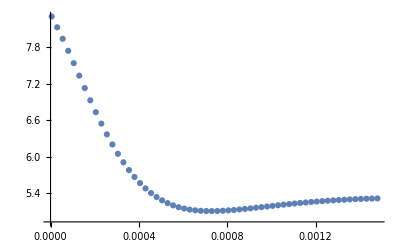

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[xi,yi,z,currents,TrapParams]/Gauss},{z,0.005mm,1.5mm,0.025mm}],PlotRange->All]
```

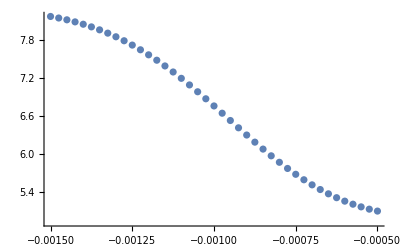

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[xi,z,zi,currents,TrapParams]/Gauss},{z,-1.5mm,-0.5mm,0.025mm}],PlotRange->All]
```

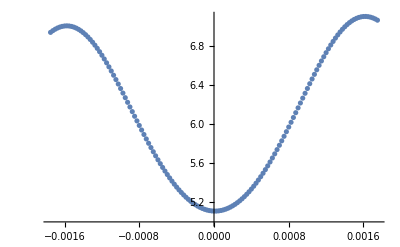

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[z,yi,zi,currents,TrapParams]/Gauss},{z,-1.75mm,+1.75mm,0.025mm}],PlotRange->All]
```

```mathematica
ListPointPlot3D[Table[1000*PE[xi,y*mm,z*mm,currents,TrapParams,0],{z,0.05,1,0.05},{y,-1.5,-0.5,0.05}],PlotRange->All]
```

-Graphics3D-

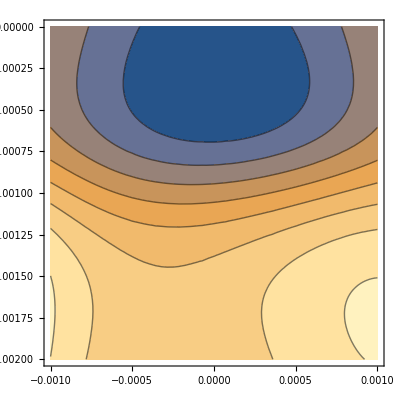

```mathematica
ContourPlot[ChipTrapFieldFAST[x,y,zi,currents,TrapParams]/Gauss,{x,-1mm,1mm},{y,-2mm,0mm}]
```

#### Ramp Sequencing from initial trap to final trap

Initial Trap : {0.85, 2.4, 2.3, -0.222, 0, 2.55, -0.15, 0}
Final IP Trap : {0., 3.2, 1., -0.729, 0, 0.765, 0., 0}

```mathematica
(*Change in each current parameter*)
ΔL = 0.85-0;
ΔZ = 2.4 - 3.2;
ΔH = 2.3 - 1.0;
ΔX = -0.222-(-0.729);
ΔY = 2.55 - 0.765;
Δz = -0.15 - 0;
```

```mathematica
(*Create a list of the current values to double check that the iterations work*)
For[i=0,i<10,i++,
frac = 1-(i*0.1);Print[{0.85-(ΔL*frac),2.4-(ΔZ*frac),2.3-(ΔH*frac),-0.222-(ΔX*frac),0,2.55-(ΔY*frac),-0.15-(Δz*frac),0}]]
```

{0.,3.2,1.,-0.729,0,0.765,0.,0}

{0.085,3.12,1.13,-0.6783,0,0.9435,-0.015,0}

{0.17,3.04,1.26,-0.6276,0,1.122,-0.03,0}

{0.255,2.96,1.39,-0.5769,0,1.3005,-0.045,0}

{0.34,2.88,1.52,-0.5262,0,1.479,-0.06,0}

{0.425,2.8,1.65,-0.4755,0,1.6575,-0.075,0}

{0.51,2.72,1.78,-0.4248,0,1.836,-0.09,0}

{0.595,2.64,1.91,-0.3741,0,2.0145,-0.105,0}

{0.68,2.56,2.04,-0.3234,0,2.193,-0.12,0}

{0.765,2.48,2.17,-0.2727,0,2.3715,-0.135,0}

```mathematica
Clear[zlist]
```

```mathematica
(* Prints minimum values, magnetic min, and frequencies to check for discontinuities*)
TrapParams = {isotope,F,mF,D1,D2,D3};

For[i=0,i<21,i++,
frac =1-(i*0.05);
currents={0.85-(ΔL*frac),2.4-(ΔZ*frac),2.3-(ΔH*frac),-0.222-(ΔX*frac),0,2.55-(ΔY*frac),-0.15-(Δz*frac),0}*A;
{xi,yi,zi}= zminFAST[currents,TrapParams,0];
Bmin = ChipTrapFieldFAST[xi,yi,zi,currents,TrapParams]/Gauss;
Freq =  ChipTrapFreqFAST[xi,yi,zi,currents,TrapParams,0];
Print[{currents, {xi,yi,zi},Bmin, Freq} ]]
```

Set::shape: Lists {xi,yi,zi} and zminFAST[{0.,3.2,1.,-0.729,0,0.765,0.,0},{Rb87,2,2,L2,Z2,H},0] are not the same shape.

{{0.,3.2,1.,-0.729,0,0.765,0.,0},{0.0000196043527,-0.0005,0.0006986299393},31.4188,{13.3328,17.964,30.1137}}

Set::shape: Lists {xi,yi,zi} and zminFAST[{0.0425,3.16,1.065,-0.70365,0,0.85425,-0.0075,0},{Rb87,2,2,L2,Z2,H},0] are not the same shape.

{{0.0425,3.16,1.065,-0.70365,0,0.85425,-0.0075,0},{0.0000196043527,-0.0005,0.0006986299393},30.7052,{13.674,21.1397,31.9325}}

Set::shape: Lists {xi,yi,zi} and zminFAST[{0.085,3.12,1.13,-0.6783,0,0.9435,-0.015,0},{Rb87,2,2,L2,Z2,H},0] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{{0.085,3.12,1.13,-0.6783,0,0.9435,-0.015,0},{0.0000196043527,-0.0005,0.0006986299393},30.0639,{13.9784,24.1761,33.8114}}

{{0.1275,3.08,1.195,-0.65295,0,1.03275,-0.0225,0},{0.0000196043527,-0.0005,0.0006986299393},29.4995,{14.2431,27.047,35.683}}

{{0.17,3.04,1.26,-0.6276,0,1.122,-0.03,0},{0.0000196043527,-0.0005,0.0006986299393},29.0165,{14.4659,29.7495,37.507}}

{{0.2125,3.,1.325,-0.60225,0,1.21125,-0.0375,0},{0.0000196043527,-0.0005,0.0006986299393},28.619,{14.6444,32.2856,39.2575}}

{{0.255,2.96,1.39,-0.5769,0,1.3005,-0.045,0},{0.0000196043527,-0.0005,0.0006986299393},28.3106,{14.7766,34.6558,40.9162}}

{{0.2975,2.92,1.455,-0.55155,0,1.38975,-0.0525,0},{0.0000196043527,-0.0005,0.0006986299393},28.0943,{14.8609,36.859,42.4695}}

{{0.34,2.88,1.52,-0.5262,0,1.479,-0.06,0},{0.0000196043527,-0.0005,0.0006986299393},27.9722,{14.8961,38.8927,43.9072}}

{{0.3825,2.84,1.585,-0.50085,0,1.56825,-0.0675,0},{0.0000196043527,-0.0005,0.0006986299393},27.9455,{14.8818,40.7536,45.222}}

{{0.425,2.8,1.65,-0.4755,0,1.6575,-0.075,0},{0.0000196043527,-0.0005,0.0006986299393},28.0145,{14.8185,42.4392,46.4091}}

{{0.4675,2.76,1.715,-0.45015,0,1.74675,-0.0825,0},{0.0000196043527,-0.0005,0.0006986299393},28.1785,{14.7071,43.9486,47.4665}}

{{0.51,2.72,1.78,-0.4248,0,1.836,-0.09,0},{0.0000196043527,-0.0005,0.0006986299393},28.4359,{14.5498,45.2831,48.3945}}

{{0.5525,2.68,1.845,-0.39945,0,1.92525,-0.0975,0},{0.0000196043527,-0.0005,0.0006986299393},28.7841,{14.3489,46.4464,49.1961}}

{{0.595,2.64,1.91,-0.3741,0,2.0145,-0.105,0},{0.0000196043527,-0.0005,0.0006986299393},29.2199,{14.1075,47.4448,49.876}}

{{0.6375,2.6,1.975,-0.34875,0,2.10375,-0.1125,0},{0.0000196043527,-0.0005,0.0006986299393},29.7395,{13.829,48.2869,50.4409}}

{{0.68,2.56,2.04,-0.3234,0,2.193,-0.12,0},{0.0000196043527,-0.0005,0.0006986299393},30.3385,{13.5169,48.9832,50.8987}}

{{0.7225,2.52,2.105,-0.29805,0,2.28225,-0.1275,0},{0.0000196043527,-0.0005,0.0006986299393},31.0124,{13.1747,49.5452,51.258}}

{{0.765,2.48,2.17,-0.2727,0,2.3715,-0.135,0},{0.0000196043527,-0.0005,0.0006986299393},31.7564,{12.8059,49.9854,51.5279}}

{{0.8075,2.44,2.235,-0.24735,0,2.46075,-0.1425,0},{0.0000196043527,-0.0005,0.0006986299393},32.5656,{12.4134,50.3164,51.7176}}

{{0.85,2.4,2.3,-0.222,0,2.55,-0.15,0},{0.0000196043527,-0.0005,0.0006986299393},33.4354,{12.0003,50.5506,51.8361}}

```mathematica
zlist
```

zlist

#### Ramping Magnetic field instead of RF frequency

Want to ramp the B field instead of the frequency of the RF, due to issues with the frequency at which we are able to do the RF ramps. Need to figure out if we have the RF frequency sitting at a particular value, what magnetic field values for the x-bias field are needed to do the ARP from the |2,2> state into the |2,1> state. 

Lets say that the code is perfect and our IP trap bottom is 31.16 G. Assuming the BR formula is giving the correct shift in the energy levels, this should lead to a state energy separation of 21.5908 MHz between the |2,2> and the |2,1> states. For the same magnetic field bottom, this yeilds a state separation of 21.7278 MHz between the |2,1> and the |2,0> states. This is a difference of 136.946 kHz. Now, if we sit at the resonant frequency for this trap bottom (21.5908 MHz), but then vary the trap bottom using the x-bias coils, what is the precision in the current that we would need to be successful in populating the |2,1> state but not the |2,0> state?

```mathematica
(*RF21[B_,iso_]:=(EnergyBR[2,2,B*Gauss,iso]-EnergyBR[2,1,B*Gauss,iso])/hPlanck/MHz;
RF10[B_,iso_]:=(EnergyBR[2,1,B*Gauss,iso]-EnergyBR[2,0,B*Gauss,iso])/hPlanck/MHz;*)
(*{RF21[58,TrapParams[[1]]],RF10[58,TrapParams[[1]]]}
{RF21[58,TrapParams[[1]]]-RF10[58,TrapParams[[1]]]}*)
(*(RF10[31.16,"Rb87"]-RF21[31.16,"Rb87"])*1000*)
```

```mathematica
currents = {3.2,-0.399*0,0,0.2645*2.685,0,2.55*0.3,0.2100*0,0}(* This is the IP TRAP!!! *)
currents = {3.2,-0.399*0,0,0.2645*2.715,0,2.55*0.3,0.2100*0,0}(* This is the IP TRAP!!! *)
(*TrapParams = {"Rb87",2,2,"Orange","Orange","None"};*)(* JDM EDITED OUT! *)

{xi,yi,zi} = zminFAST[currents,TrapParams,0]
Bmin = ChipTrapFieldFAST[xi,yi,zi,currents,TrapParams]/Gauss

{RF21[Bmin,TrapParams[[1]]]-21.5904,RF10[Bmin,TrapParams[[1]]]-21.5904}
```

{3.2,0.,0,0.710183,0,0.765,0.,0}

{3.2,0.,0,0.718118,0,0.765,0.,0}

Set::shape: Lists {xi,yi,zi} and zminFAST[{3.2,0.,0,0.718118,0,0.765,0.,0},{Rb87,2,2,Orange,Orange,None},0] are not the same shape.

zminFAST[{3.2,0.,0,0.718118,0,0.765,0.,0},{Rb87,2,2,Orange,Orange,None},0]

10000 ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None.

{-21.5904+RF21[10000 ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None.,Rb87],-21.5904+RF10[10000 ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None.,Rb87]}

```mathematica
{3.2*(0.914/3.2),-0.399*(0.914/3.2),0,0.2645*(-0.0319/0.2645),0,2.55*(0.83/2.55),0.2100*(-0.07/0.2100),0}
{3.2*(0.914/3.2),0*-0.399*(0.914/3.2),0,2.7*0.2645*(-0.0319/0.2645),0A,0.3*2.55*(0.83/2.55),0*0.2100*(-0.07/0.2100),0A}
```

{0.914,-0.113964,0,-0.0319,0,0.83,-0.07,0}

{0.914,0.,0,-0.08613,0,0.249,0.,0}

```mathematica
Plot[ChipTrapFieldFAST[0,0,z,currents,TrapParams]/Gauss,{z,0.300mm,0.900mm}]
```

-Graphics-

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[0,0,z,{3.5,0,0,0,0,7/14.286,0,0},TrapParams]/Gauss},{z,0.01mm,3mm,0.05mm}],PlotRange->All]
```

-Graphics-

```mathematica
(*f[{x_,y_}]:=ChipTrapFieldFAST[x mm,y mm,zi,currents,TrapParams]/Gauss;
ContourPlot[{f[{x,y}]==31.5,f[RotationTransform[-24Degree,{xi,yi}][{x,y}]]==31.5},{x,-0.5,0.5},{y,-0.5,0.5}]*)
```

```mathematica
(*TrapParams = {isotope,F,mF,D1,D2,D3};
zlist = {};
For[i=0,i<10,i++,
factor = 1-(i*0.1);
currents={0.4,-1.2,0,factor*0.4,0,factor*0.7,0,0}*A;
(*currents ={0.4428A,0.00,0,i/14*0.7627,0A,0.4675,0A,0A};*)
{xi,yi,zi}= zmin[currents,TrapParams,0];
zlist = Append[zlist,zi];]
(*For[i=1,i<8,i++,
factor=1-(i*0.1);
currents={0.4,-1.2,0,factor*0.04,0,0.07,0,0}*A;
{xi,yi,zi}= zmin[currents,TrapParams,0];
zlist = Append[zlist,zi];]*)
*)
```

```mathematica
(*RampPics={};
For[i=0,i<10,i++,
factor = 1-(i*0.1);
currents={0.4,-1.2,0,factor*0.4,0,factor*0.7,0,0}*A;
AdiaRamp = ContourPlot[ChipTrapFieldFAST[x mm,y mm,zlist[[i+1]],currents,TrapParams]/Gauss,{x,-1,1},{y,-1,1},Contours->20];
RampPics=AppendTo[RampPics,AdiaRamp];]
For[i=0,i<8,i++,
factor = 1-(i*0.1);
currents={0.4,-1.2,0,factor*0.04,0,0.07,0,0}*A;
AdiaRamp = ContourPlot[ChipTrapFieldFAST[x mm,y mm,zlist[[i+11]],currents,TrapParams]/Gauss,{x,-1,1},{y,-1,1},Contours->20];
RampPics=AppendTo[RampPics,AdiaRamp];]*)
```

```mathematica
(*Export["SecondEfimovRamp.gif",RampPics,"DisplayDurations"-> 1];*)
```

#### Attempting to Optimize...

```mathematica
(*list = {{0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {1, 1, 1, 1, 0, 0}, {1, 1, 1, 1, 1, 0}, {1, 1, 1, 1, 1, 1}};
list1 = Permutations[list[[1]]];
list2 = Permutations[list[[2]]];
list3 = Permutations[list[[3]]];
list4 = Permutations[list[[4]]];
list5 = Permutations[list[[5]]];
list6 = Permutations[list[[6]]];
list7 = Permutations[list[[7]]];
listTOT =  Join[list1, list2, list3, list4, list5, list6, list7];*)
```

```mathematica
(*BestFitFunct[id1_, id2_, iT_, iM_, iY_, iZ_] := Module[{factor, xi, yi, zi, Bmin, result},
  result = ConstantArray[0, {64, 2}];
  For[i = 1, i < 3, i++,
    factor = (-1)^listTOT[[i]];
    id1 = id1*factor[[1]];
    id2 = id2*factor[[2]];
    iT = iT*factor[[3]];
    iM = iM*factor[[4]];
    iY = iY*factor[[5]];
    iZ = iZ*factor[[6]];
    {xi, yi, zi} = zminTRAP[id1, id2, iT, iM, iY, iZ, 0, 1];
    xi = xi[[2]];
    yi = yi[[2]];
    zi = zi[[2]];
    Bmin = ChipTrapField[xi, yi, zi, id1, id2, iT, iM, iY, iZ, 0];
    result[[i]][[1]] = factor;
    result[[i]][[2]] = Bmin;
    ]
   Return[result]
  ]
*)
```

```mathematica
(*For[i = 1, i < 65, i++,
 factor = (-1)^listTOT[[i]];
 {xi, yi, zi} = zminTRAP[factor[[1]]*iD1, factor[[2]]*iD2, factor[[3]]*iTtrap, factor[[4]]*iMtrap, factor[[5]]*iYtrap, factor[[6]]*iZtrap, iFFtrap, 1];
 xi = xi[[2]];
 yi = yi[[2]];
 zi = zi[[2]];
 Bmin = ChipTrapField[xi, yi, zi, factor[[1]]*iD1, factor[[2]]*iD2, factor[[3]]*iTtrap, factor[[4]]*iMtrap, factor[[5]]*iYtrap, factor[[6]]*iZtrap, iFFtrap];
 Print[{{factor}, {xi, yi, zi}, Bmin}]
 ]*)
```

#### Checking bias field values

```mathematica
convertCALTableToTrapParameters[tableZHbB3]
```

{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335}

```mathematica
printTrapParameters@convertCALTableToTrapParameters@tableZHbB3
```

CurrLa | 0.
CurrZa | 0
CurrLb | 0.
CurrZb | 2.425
CurrH | 2.6
Bx1 | -1.95
By1 | 3.55435
Bz1 | -3.11335

```mathematica
(*{iD1,iD2,iD3,iT,iM,iY,iZ,iFF}*)
testPt={40,684-1000,646}*10^(-6);
xBiasOnly={0,0,0,-#[[4]],0,0,0,0}&[convertCurrentsBToME@convertCALTableToCurrents@tableZHbB3]
yBiasOnly={0,0,0,0,0,#[[6]],0,0}&[convertCurrentsBToME@convertCALTableToCurrents@tableZHbB3]
zBiasOnly={0,0,0,0,0,0,-#[[7]],0}&[convertCurrentsBToME@convertCALTableToCurrents@tableZHbB3]
```

{0,0,0,-0.048,0,0,0,0}

{0,0,0,0,0,0.2488,0,0}

{0,0,0,0,0,0,-0.300285,0}

```mathematica
(* X bias prediction is roughly the same *)
MagTrapVecField[testPt[[1]],testPt[[2]],testPt[[3]],xBiasOnly,TrapParams]/Gauss
(* Y bias prediction is roughly the same *)
MagTrapVecField[testPt[[1]],testPt[[2]],testPt[[3]],yBiasOnly,TrapParams]/Gauss
(* Z bias has opposite sign *)
MagTrapVecField[testPt[[1]],testPt[[2]],testPt[[3]],zBiasOnly,TrapParams]/Gauss
```

{-2.0238,0.0000524517,-0.000205317}

{0.000160936,3.50355,0.00144963}

{0.0191514,-0.000864035,-2.96002}

```mathematica
MagTrapVecField[x_,y_,z_,currents_,trapparams_]:=Module[{d1,d2,d3,iD1,iD2,iD3,iT,iM,iY,iZ,iFF,drive1,drive2,drive3,VecField,transfer,MOT,Ybias,Zbias,FF,Gravity},
iD1 = currents[[1]];
iD2 = currents[[2]];
iD3 = currents[[3]];
iT = currents[[4]];
iM = currents[[5]];
iY = currents[[6]];
iZ = currents[[7]];
iFF = currents[[8]];
d1 = trapparams[[4]];
d2 = trapparams[[5]];
d3 = trapparams[[6]];
transfer = BiasCoils[TransferCoils[iT]];
MOT = BiasCoils[MOTCoils[iM]];
Ybias = BiasCoils[YbiasCoils[iY]];
Zbias = BiasCoils[ZbiasCoils[iZ]];
FF=BiasCoils[FFCoils[iFF]];

drive1 =  Which[
d1=="Z1",(Ywire[x,y,z,WireWidth,Za[[1]]]+Xwire[x,y,z,WireWidth,Za[[2]]]+Ywire[x,y,z,WireWidth,Za[[3]]]),
d1=="L2",(Ywire[x,y,z,WireWidth,Lb[[2]]]+Xwire[x,y,z,WireWidth,Lb[[2]]]+Ywire[x,y,z,WireWidth,Lb[[3]]]),
d1=="T2",(Ywire[x,y,z,WireWidth,Tb[[1]]]+Xwire[x,y,z,WireWidth,Tb[[2]]]+Ywire[x,y,z,WireWidth,Tb[[3]]]),
d1=="Z2", Return["Z2 is not a valid option for driver 1. Please choose Z1, L2, T2 or None."],
d1=="L1", Return["L1 is not a valid option for driver 1. Please choose Z1, L2, T2 or None."],
d1=="FF", Return["FF is not a valid option for driver 1. Please choose Z1, L2, T2 or None."],
d1=="H", Return["H is not a valid option for driver 1. Please choose Z1, L2, T2 or None."],
d1!="Z1"∨"L2"∨"T2"∨"Z2"∨"L1"∨"FF"∨"H", Return["ERROR. The wire name you entered for 
driver 1 does not exist in this program. Valid wire names for driver 1 are Z1, L2, T2 or None."],
d1=="None",0];

drive2 = Which[
d2=="Z2",(Ywire[x,y,z,WireWidth,Zb[[1]]]+Xwire[x,y,z,WireWidth,Zb[[2]]]+Ywire[x,y,z,WireWidth,Zb[[3]]]),
d2=="L1",(Ywire[x,y,z,WireWidth,La[[1]]]+Xwire[x,y,z,WireWidth,La[[2]]]+Ywire[x,y,z,WireWidth,La[[3]]]),
d2=="FF",0,
d2=="Z1", Return["Z1 is not a valid option for driver 2. Please choose Z2, L1, FF or None."],
d2=="L2", Return["L2 is not a valid option for driver 2. Please choose Z2, L1, FF or None."],
d2=="T2", Return["T2 is not a valid option for driver 2. Please choose Z2, L1, FF or None."],
d2=="H", Return["H is not a valid option for driver 2. Please choose Z2, L1, FF or None."],
d2!="Z1"∨"L2"∨"T2"∨"Z2"∨"L1"∨"FF"∨"H", Return["ERROR. The wire name you entered for 
driver 2 does not exist in this program. Valid wire names for driver 2 are Z2, L1, FF or None."],
d2=="None",0];

drive3 = Which[
d3=="H",(Ywire[x,y,z-Hoffset,200μm,Ha[[1]]]+Ywire[x,y,z-Hoffset,200μm,Hb[[1]]]),
d3=="Z1", Return["Z1 is not a valid option for driver 3. Please choose H or None."],
d3=="L2", Return["L2 is not a valid option for driver 3. Please choose H or None."],
d3=="T2", Return["T2 is not a valid option for driver 3. Please choose H or None."],
d3=="Z2", Return["Z2 is not a valid option for driver 3. Please choose H or None."],
d3=="L1", Return["L1 is not a valid option for driver 3. Please choose H or None."],
d3=="FF", Return["FF is not a valid option for driver 3. Please choose H or None."],
d3!="Z1"∨"L2"∨"T2"∨"Z2"∨"L1"∨"FF"∨"H", Return["ERROR. The wire name you entered for 
driver 3 does not exist in this program. Valid wire names for driver 3 are H or None."],
d3=="None",0];

VecField = iD1*drive1 + iD2*drive2 + iD3*drive3 + {BzSum[x,y,z,transfer,MOT,Ybias,Zbias,FF],BxSum[x,y,z,transfer,MOT,Ybias,Zbias,FF],BySum[x,y,z,transfer,MOT,Ybias,Zbias,FF]};
Return[VecField]
]
```